```mathematica
(*Poisson solver that implements the first part of the algorithm described below - it represents the Laplacian as a matrix operator then inverts it. Any solution to Poisson's equation is now found by multiplying the inverse matrix by the (forcing function ρ? idk if you can call it that)*)
(*This is a finite difference method to solve the Poisson Equation*) 
(*en.wikipedia.org/wiki/Discrete_Poisson_equation*)
Clear[MM,NN,λ] 


MM= 40;(*Increases accuracy*)
NN=20;(*Pulls it back*)


(*construct D, the matrix operator that corresponds to the Laplacian. This is a 9 point stencil*)
periodicblock[a_,b_]:=a IdentityMatrix[MM-1]+DiagonalMatrix[Table[b,{i,0,MM-3}],1]+DiagonalMatrix[Table[b,{i,0,MM-3}],-1]+DiagonalMatrix[{b},-MM+2]+DiagonalMatrix[{b},MM-2];
m1 = periodicblock[-2./3,-1/6];
m2 = periodicblock[10/3,-2/3];
m3 =KroneckerProduct[DiagonalMatrix[Join[Table[1,{i,1,NN}],{0}],0],m2];
m4 =KroneckerProduct[DiagonalMatrix[Join[Table[1,{i,1,NN-1}],{0}],1],m1];
m5 =KroneckerProduct[DiagonalMatrix[Join[Table[1,{i,1,NN-1}],{0}],-1],m1];
m6 =KroneckerProduct[DiagonalMatrix[{1},NN],m1];
m7=1/2 IdentityMatrix[MM-1];
m8 =KroneckerProduct[DiagonalMatrix[{0,1},-NN+1],-m7];
m9=KroneckerProduct[DiagonalMatrix[Join[Table[0,{i,1,NN}],{1}],0],m7];
m = m3+m4+m5+m6+m8+m9;
newm=m3+m4+m5;


ϵ1=10;
ϵ2=5;
H=3.074;(*In terms of unit cells*)
γ=10;
α=.0215748;(*Subscript[ϵ, 0]/e*)
λ=10N[π];

totalCharge= -α ϵ2 γ MM;

chargeDist[x_,y_]:=1;(*(x^2+(y-MM/2)^2)^(1/2)*)(*If[y==MM/2&&x==3,1,0]*)

tempTotal = Table[
 N[chargeDist[i ,j ]],
{i,1,NN},
{j,1,MM-1}
]//Flatten//Total;

n[x_,y_]:= -1/(α ϵ2)chargeDist[x,y]/tempTotal totalCharge;(*Charge distribution*)
e1[y_]:=γ;(*Normal component of electric field at top edge of the grid (λ H)/(2 N[π]ϵ1(H^2+(y-MM/2)^2))*)


(*Defines the list with the charge distribution Subscript[ρ, ij] generated from the user, augmented with the boundary conditions *)
chargeVector  = Flatten[
Table[
 n[i ,j ],
{i,1,NN},
{j,1,MM-1}
]
];
exteriorPoints = Flatten[
Table[
 -  N[e1[j ]] ,
{j,1,MM-1}
]
];
chargeVector = Join[chargeVector, exteriorPoints];
chargeVector=chargeVector-1/2 newm.chargeVector;
(*Calculates the potential*)
potential = LinearSolve[m,chargeVector];

(*Gives the total potential in order to plot it. This includes the portion computed by the matrix solver and the periodic boundary. First it adds the calculated potential, then the periodic boundary which wasn't solved for*)
plotList  = Flatten[
Table[
{i ,j ,potential[[j + (MM-1)(i-1)]]},
{i,1,NN},
{j,1,MM-1}
],1
];
periodicEdge = 
Table[
{i ,MM  ,potential[[1 + (MM-1)(i-1)]]},
{i,1,NN}
];
plotList = Join[plotList, periodicEdge];

(*Generates the data on user inputted charge distribution to plot*)
chargeDistributionList  = Flatten[
Table[
 {i, j,n[i ,j ]},
{i,1,NN},
{j,1,MM-1}
],1
];

(*Plots the charge distribution, then the resulting potential*)
ListPlot3D[chargeDistributionList, PlotLabel->"Charge Distribution", PlotRange->All]
ListPlot3D[plotList,PlotRange->All,PlotLabel->"Calculated Electric Potential",PlotRange->All]
```

-Graphics3D-

-Graphics3D-

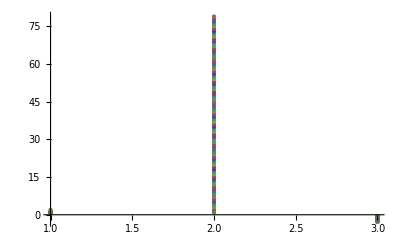

```mathematica
ListPlot[plotList[[1;;80,;;]]]
```

```mathematica
plotList[[1;;80,;;]]
```

```mathematica
totalCharge
```

-43.1496

```mathematica
n[1,20]
```

400.